```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample"];
teldData=ReadList["T0.1_T0.328eV_eltempdiff.dat",{Number, Number,Number,Number}];
(*F 0.1 E0 0.1 then F 0.328 E0 0.328*)
```

```mathematica
f01=Transpose[teldData][[1]]-teldData[[1]][[1]];
e001=Transpose[teldData][[2]]-teldData[[1]][[2]];
f03=Transpose[teldData][[3]]-teldData[[1]][[3]];
e003=Transpose[teldData][[4]]-teldData[[1]][[4]];
```

```mathematica
Table[StandardDeviation[{f01,e001,f03,e003}[[i]]],{i,1,4}]
Table[Mean@{f01,e001,f03,e003}[[i]],{i,1,4}]
```

{4.25742,4.26829,4.1492,4.26119}

{30.3456,30.3903,29.6628,30.4663}

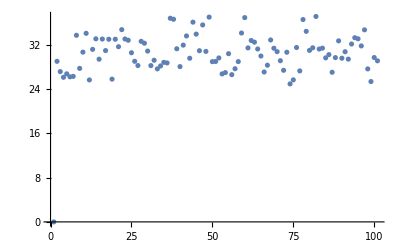

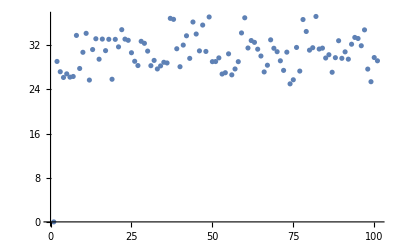

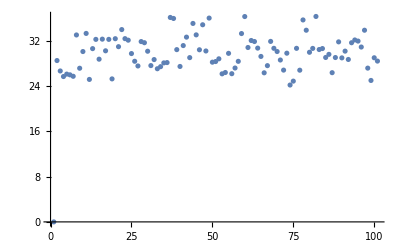

```mathematica
ListPlot[f01]
ListPlot[e001]
ListPlot[f03]
```